```mathematica
Clear[s]
```

```mathematica
muf[m_,N_]:=m*N/(m+N)
s[m_,N_,g_]:=muf[m,N]^2*54/Pi * (g^2/(62Pi^ 2 m^2)*(1+2/3Log[1/m^2]))^2
sigm1308[m_,N_,g_]:=muf[m,N]^2 * 3/(16Pi^ 2) * g^4 /(m^2-(m+800)^2)^2
```

```mathematica
Plot[s[m,127,1],{m,0,400}];
```

```mathematica
r[m_]:=4m*100 /(m+100)^2
```

```mathematica
F[Q_]:=(BesselJ[1,Q]/Q)^2*Exp[-Q^2]
Plot[NIntegrate[F[Q],{Q,0,x}],{x,0,10}];
NIntegrate[F[Q],{Q,0,10}];
```

```mathematica
Plot[F[Q],{Q,0,1}];
```

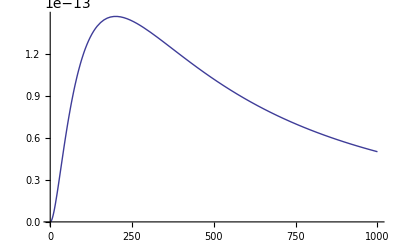

```mathematica
Plot[1/(x^2-(x+100)^2)^2,{x,1,1000}];
Plot[((x*100/(x+100))^2)/(x+200)^4,{x,1,1000}];
Plot[sigm1308[x,100,0.2],{x,1,1000}]
```

```mathematica
8/(9*192)
216/16
```

1/216

27/2

```mathematica
e = 0.2;
gu = 0.008;
gd = 0.008;
gs = 0.04;
gc = 0.04;
gb = 1;
gt = 1;
binolike 1007.2601
fu = 0.02; (*susyreview*)
fd = 0.026;
fs = 0.14;
fG = 1-(fu+fd+fs);
u2=0.22;
d2=0.11;
s2=0.026;
c2=0.019;
b2=0.012;
ub2=0.034;
db2=0.036;
sb2=s2;
cb2=c2;
bb2=b2;

mu = 2.3*^-3;
md = 4.8*^-3;
ms = 95*^-3;
mc = 1.275;
mb = 4.18;
mt = 173;

mp=1;
A = 137;
mr[mChi_,N_]:=mChi*N*mp/(mChi+N*mp);
r[mChi_,N_]:=4*mr[mChi,N]/(mChi+N*mp);
Clear[sigma]
```

1007.26 binolike

```mathematica
f1=1/16*(gu^ 2*fu+gd^ 2fd+gs^ 2fs)
f2=1/216*(gu^ 2+gd^ 2+gs^ 2+gc^ 2+gb^ 2+gt^ 2)fG
f3=3/16 ((u2+ub2)gu^ 2 +(d2+db2)gd^ 2 +(s2+sb2)gs^ 2 +(c2+cb2)gc^ 2 +(b2+bb2)gb^ 2)
f[m_]:=(f1+f2+f3)*m/(m+1000)^4
```

0.000014184

0.00754958

0.0045318

```mathematica
sigma1007[m_]:=4/Pi * mr[m,A]^2*(A*f[m])^2
45-27
```

18

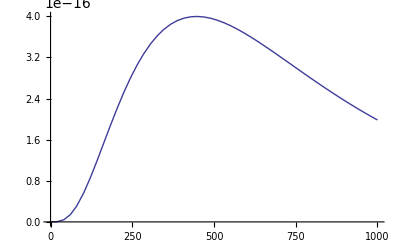

```mathematica
Plot[{sigma1007[m]},{m,0,1000}]
```